In the present file we develop and write matrices corresponding to 1D moment systems.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity2[a_,filename_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]]-1,{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]]-1,{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["../system_matrices/",filename]];

WriteString[str,ToString[nnz],"\n"];

Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

(*first we write the number of entries in the vector*)
NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
(*The care regarding C indices has already been taken off in the main routine*)
Do[WriteString[str,ToString[vec[[ii]]],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

(*Distribution with respect to L2*)
H2[i_,c_]=(1 2^(1/4) (2π)^(1/4))/(√Gamma[i+1] 2^(i/2))HermiteH[i,c];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
fL2[c_,n_]:=∑_(k=0)^(n-1) α[k]H2[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*Simplified expression for half space integral *)
ExplicitHSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(m!))/(√(n!))(∑_(p=1)^n 1/((p-m-2)!! (1-p+m)! (p-n-1)!!)+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

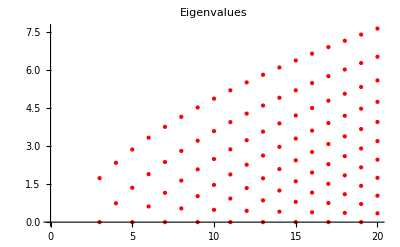

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal. α[2] = θW/(√2)*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]

(*Boe matrix for the inflow boundary conditions.*)
MatBoeInflow[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];

(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal. α[2] = θW/(√2)*)
Do[result⟦ii⟧=2(∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

(*Following the notation in the boundary condition paper, this is \hat{M}^(mbc)*)
Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;

(*We now develop the Onsager matrix using the Maxwell's accommodation model*)
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]

MatOnsagerInflow[n_]:=Module[{Btilde,result,Boe,Aoe},
Boe = MatBoeInflow[n];
Aoe = MatAoe[n];

(*Following the notation in the boundary condition paper, this is \hat{M}^(mbc)*)
Btilde=Boe⟦All,1;;Length[Boe]⟧;

(*We now develop the Onsager matrix using the Maxwell's accommodation model*)
Btilde.Inverse[Aoe⟦All,1;;Length[Aoe]⟧]
]
```

## Final Matrices

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

### Checks for properties of a matrix

```mathematica
CheckSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

(*check for the symmetricity of the matrices by computing A - Transpose[A]*)
If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

(*compute the positive definetness by computing the eigenvalues*)
If[Length[Select[EV,#<=0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]
```

### Core Routine

```mathematica
Clear[α]
```

```mathematica
FinalMatrices1D[Ntensors_]:=Module[{Ax,Boe,var,varRearranged,IDEven,IDOdd,OddVar,EvenVar,B,PermuteMat,PermuteMatInv,Sigma,nEqn,nBC,OnsagerMat,OnsagerMatInflow,BoeInflow,BInflow,filenameAx,filenameAy,filenameB,filenameOddID,filenameSigma,filenameBinflow,$MaxExtraPrecision=150,precision = 15},

(*we first develop the system matrix. *)
Ax = AA[Ntensors];

(*Develop all the variables needed by the present routine*)
var = Map[α[#]&,Range[0,Ntensors-1,1]];(*total number of variables = Ntensors*)
IDOdd = If[EvenQ[Ntensors],Range[1,Ntensors-1,2],Range[1,Ntensors-2,2]]; (*ID of the odd variables.*)
IDEven = If[EvenQ[Ntensors],Range[0,Ntensors-2,2],Range[0,Ntensors-1,2]];(*ID of the even variables.*)
OddVar=Map[α[#]&,IDOdd];(*Odd variables*)
EvenVar=Map[α[#]&,IDEven];(*Even variables*)
nEqn = Length[var];(*total number of equations*)
nBC = Length[OddVar];(*total number of boundary conditions*)
varRearranged = Join[OddVar,EvenVar];(*rearranged solution vector with odd variables first and then even variables*)
PermuteMat = PermuteVar[var,varRearranged];(*var = PermuteMat * varRearranged*)
PermuteMatInv = PermuteVar[varRearranged,var];(*varRearranged = PermuteMatInv * var*)

(*Computation of the Onsager matrix along with the fix for the normal velocity. *)
OnsagerMat = MatOnsager[Ntensors];
OnsagerMat⟦1,1⟧=1;
OnsagerMatInflow = MatOnsagerInflow[Ntensors];

CheckSPD[OnsagerMat,"Onsager matrix"];
CheckSPD[OnsagerMatInflow,"Onsager matrix Inflow"];

(*boundary conditions of the form Uo = Boe*Ue. From the Maxwell's accommodatio model. *)
Boe = OnsagerMat.MatAoe[Ntensors];
BoeInflow = OnsagerMatInflow.MatAoe[Ntensors];

B = ConstantArray[0,{Length[OddVar],Length[var]}];
B⟦1;;All,1;;Length[IDOdd]⟧ = IdentityMatrix[Length[IDOdd]];(*Boundary matrix in the form B.U = g where U is rearranged*)
B⟦1;;All,(Length[IDOdd]+1);;-1⟧ = - Boe;
B = B.PermuteMatInv;(*Return back to the normal variables*)

BInflow = ConstantArray[0,{Length[OddVar],Length[var]}];
BInflow⟦1;;All,1;;Length[IDOdd]⟧ = IdentityMatrix[Length[IDOdd]];(*Boundary matrix in the form B.U = g where U is rearranged*)
BInflow⟦1;;All,(Length[IDOdd]+1);;-1⟧ = - BoeInflow;
BInflow = BInflow.PermuteMatInv;(*Return back to the normal variables*)


(*Penalty matrix for the weak implementation of the boundary conditions*)
Sigma = ConstantArray[0,{nEqn,nBC}];
Sigma⟦-Length[IDEven];;-1,All⟧ = Transpose[MatAoe[Ntensors]];(*the first few columns of sigma *)
Sigma = Transpose[PermuteMatInv].Sigma;(*Appropriate permuation*)

(*write out the matrices to the file*)
filenameAx=StringJoin["A1_1D_",ToString[nEqn],".txt"];
filenameB=StringJoin["B_1D_",ToString[nEqn],".txt"];
filenameOddID=StringJoin["odd_ID_1D_",ToString[nEqn],".txt"];
filenameSigma = StringJoin["Sigma_1D_",ToString[nEqn],".txt"];
filenameBinflow = StringJoin["Binflow_1D_",ToString[nEqn],".txt"];

developsparsity2[N[Ax,precision],filenameAx];
Print[Style[filenameAx,FontColor->Black]];
developsparsity2[N[B,precision],filenameB];
Print[Style[filenameB,FontColor->Black]];
writeVector[IDOdd,filenameOddID];
Print[Style[filenameOddID,FontColor->Black]];
developsparsity2[N[Sigma,precision],filenameSigma];
Print[Style[filenameSigma,FontColor->Black]];
developsparsity2[N[BInflow,precision],filenameBinflow];
Print[Style[filenameBinflow,FontColor->Black]];

{Ax,B,BInflow}
]
```

## Results

### G20

```mathematica
Ntensors = 6;
{Ax1D20,B1D20,BInflow1D20}=FinalMatrices1D[6];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_6.txt

B_1D_6.txt

odd_ID_1D_6.txt

Sigma_1D_6.txt

Binflow_1D_6.txt

### G26

```mathematica
Ntensors = 8;
{Ax1D26,B1D26,BInflow1D26}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_8.txt

B_1D_8.txt

odd_ID_1D_8.txt

Sigma_1D_8.txt

Binflow_1D_8.txt

### G35

```mathematica
Ntensors = 9;
{Ax1D35,B1D35,BInflow1D35}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_9.txt

B_1D_9.txt

odd_ID_1D_9.txt

Sigma_1D_9.txt

Binflow_1D_9.txt

### G45

```mathematica
Ntensors = 11;
{Ax1D45,B1D45,BInflow1D45}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_11.txt

B_1D_11.txt

odd_ID_1D_11.txt

Sigma_1D_11.txt

Binflow_1D_11.txt

### G56

```mathematica
Ntensors = 12;
{Ax1D56,B1D56,BInflow1D56}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_12.txt

B_1D_12.txt

odd_ID_1D_12.txt

Sigma_1D_12.txt

Binflow_1D_12.txt

### N14

```mathematica
Ntensors = 14;
{Ax1D,B1D,BInflow1D}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_14.txt

B_1D_14.txt

odd_ID_1D_14.txt

Sigma_1D_14.txt

Binflow_1D_14.txt

### N16

```mathematica
Ntensors = 16;
{Ax1D,B1D,BInflow1D}=FinalMatrices1D[Ntensors];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_16.txt

B_1D_16.txt

odd_ID_1D_16.txt

Sigma_1D_16.txt

Binflow_1D_16.txt

### All even systems

```mathematica
Ntensors = Range[6,24,2];
Table[FinalMatrices1D[ii],{ii,Ntensors}];
```

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_6.txt

B_1D_6.txt

odd_ID_1D_6.txt

Sigma_1D_6.txt

Binflow_1D_6.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_8.txt

B_1D_8.txt

odd_ID_1D_8.txt

Sigma_1D_8.txt

Binflow_1D_8.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_10.txt

B_1D_10.txt

odd_ID_1D_10.txt

Sigma_1D_10.txt

Binflow_1D_10.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_12.txt

B_1D_12.txt

odd_ID_1D_12.txt

Sigma_1D_12.txt

Binflow_1D_12.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_14.txt

B_1D_14.txt

odd_ID_1D_14.txt

Sigma_1D_14.txt

Binflow_1D_14.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_16.txt

B_1D_16.txt

odd_ID_1D_16.txt

Sigma_1D_16.txt

Binflow_1D_16.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_18.txt

B_1D_18.txt

odd_ID_1D_18.txt

Sigma_1D_18.txt

Binflow_1D_18.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_20.txt

B_1D_20.txt

odd_ID_1D_20.txt

Sigma_1D_20.txt

Binflow_1D_20.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_22.txt

B_1D_22.txt

odd_ID_1D_22.txt

Sigma_1D_22.txt

Binflow_1D_22.txt

Onsager matrix

Symmetric

Positive Definite

Onsager matrix Inflow

Symmetric

Positive Definite

A1_1D_24.txt

B_1D_24.txt

odd_ID_1D_24.txt

Sigma_1D_24.txt

Binflow_1D_24.txt